```mathematica
data={{0,1},{1,2},{2,3},{3,4},{4,5},{5,8},{6,5}}
```

{{0,1},{1,2},{2,3},{3,4},{4,5},{5,8},{6,5}}

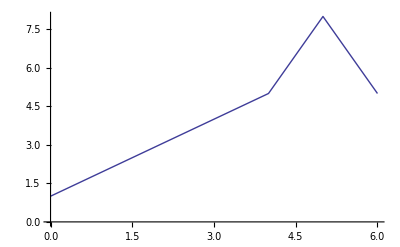

```mathematica
ListPlot[data,Joined->True]
```

```mathematica
f=Interpolation[data]
```

InterpolatingFunction[{{0,6}},<>]

```mathematica
f[2.5]
```

3.5

```mathematica
data2={{{2,2},3},{{2,3},3},{{2,4},6},{{2,5},6},{{2,6},10},{{2,7},9},{{2,8},15},{{2,9},14},{{3,3},7},{{3,4},16},{{3,5},30},{{4,4},53}}
```

{{{2,2},3},{{2,3},3},{{2,4},6},{{2,5},6},{{2,6},10},{{2,7},9},{{2,8},15},{{2,9},14},{{3,3},7},{{3,4},16},{{3,5},30},{{4,4},53}}

```mathematica
data2p=ArrayReshape[data2,{Length[data2],3}]
```

{{2,2,3},{2,3,3},{2,4,6},{2,5,6},{2,6,10},{2,7,9},{2,8,15},{2,9,14},{3,3,7},{3,4,16},{3,5,30},{4,4,53}}

```mathematica
ListPlot3D[data2p]
```

-Graphics3D-

```mathematica
f2=Interpolation[data2]
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

Interpolation::umprec: Interpolation on unstructured grids is currently only supported for machine numbers. The data will be coerced to machine precision.

InterpolatingFunction[{{2.,4.},{2.,9.}},<>]

```mathematica
f2b=Interpolation[data2,InterpolationOrder->1]
```

Interpolation::umprec: Interpolation on unstructured grids is currently only supported for machine numbers. The data will be coerced to machine precision.

InterpolatingFunction[{{2.,4.},{2.,9.}},<>]

```mathematica
f2[2.5,3.5]
```

6.5

```mathematica
f2b[2,3]
```

3.

```mathematica
xc=Table[xcv,{xcv,-3,3}]
```

{-3,-2,-1,0,1,2,3}

```mathematica
yc=Table[ycv,{ycv,-3,3}]
```

{-3,-2,-1,0,1,2,3}

```mathematica
ftest[x_,y_]:=Sin[x]+Cos[y]+I x y
```

```mathematica
ftest[2,3]
```

6 ⅈ+Cos[3]+Sin[2]

```mathematica
Plot3D[Re[ftest[x,y]],{x,-3,3},{y,-3,3}]
```

-Graphics3D-

```mathematica
Plot3D[Im[ftest[x,y]],{x,-3,3},{y,-3,3}]
```

-Graphics3D-

```mathematica
data3=Flatten[Table[{{xc[[i]],yc[[j]]},N[ftest[xc[[i]],yc[[j]]]]},{i,1,Length[xc]},{j,1,Length[yc]}],1]
```

{{{-3,-3},-1.13111+9. ⅈ},{{-3,-2},-0.557267+6. ⅈ},{{-3,-1},0.399182+3. ⅈ},{{-3,0},0.85888},{{-3,1},0.399182-3. ⅈ},{{-3,2},-0.557267-6. ⅈ},{{-3,3},-1.13111-9. ⅈ},{{-2,-3},-1.89929+6. ⅈ},{{-2,-2},-1.32544+4. ⅈ},{{-2,-1},-0.368995+2. ⅈ},{{-2,0},0.0907026},{{-2,1},-0.368995-2. ⅈ},{{-2,2},-1.32544-4. ⅈ},{{-2,3},-1.89929-6. ⅈ},{{-1,-3},-1.83146+3. ⅈ},{{-1,-2},-1.25762+2. ⅈ},{{-1,-1},-0.301169+1. ⅈ},{{-1,0},0.158529},{{-1,1},-0.301169-1. ⅈ},{{-1,2},-1.25762-2. ⅈ},{{-1,3},-1.83146-3. ⅈ},{{0,-3},-0.989992},{{0,-2},-0.416147},{{0,-1},0.540302},{{0,0},1.},{{0,1},0.540302},{{0,2},-0.416147},{{0,3},-0.989992},{{1,-3},-0.148522-3. ⅈ},{{1,-2},0.425324-2. ⅈ},{{1,-1},1.38177-1. ⅈ},{{1,0},1.84147},{{1,1},1.38177+1. ⅈ},{{1,2},0.425324+2. ⅈ},{{1,3},-0.148522+3. ⅈ},{{2,-3},-0.0806951-6. ⅈ},{{2,-2},0.493151-4. ⅈ},{{2,-1},1.4496-2. ⅈ},{{2,0},1.9093},{{2,1},1.4496+2. ⅈ},{{2,2},0.493151+4. ⅈ},{{2,3},-0.0806951+6. ⅈ},{{3,-3},-0.848872-9. ⅈ},{{3,-2},-0.275027-6. ⅈ},{{3,-1},0.681422-3. ⅈ},{{3,0},1.14112},{{3,1},0.681422+3. ⅈ},{{3,2},-0.275027+6. ⅈ},{{3,3},-0.848872+9. ⅈ}}

```mathematica
data3p=ArrayReshape[data3,{Length[data3],3}]
```

{{-3,-3,-1.13111+9. ⅈ},{-3,-2,-0.557267+6. ⅈ},{-3,-1,0.399182+3. ⅈ},{-3,0,0.85888},{-3,1,0.399182-3. ⅈ},{-3,2,-0.557267-6. ⅈ},{-3,3,-1.13111-9. ⅈ},{-2,-3,-1.89929+6. ⅈ},{-2,-2,-1.32544+4. ⅈ},{-2,-1,-0.368995+2. ⅈ},{-2,0,0.0907026},{-2,1,-0.368995-2. ⅈ},{-2,2,-1.32544-4. ⅈ},{-2,3,-1.89929-6. ⅈ},{-1,-3,-1.83146+3. ⅈ},{-1,-2,-1.25762+2. ⅈ},{-1,-1,-0.301169+1. ⅈ},{-1,0,0.158529},{-1,1,-0.301169-1. ⅈ},{-1,2,-1.25762-2. ⅈ},{-1,3,-1.83146-3. ⅈ},{0,-3,-0.989992},{0,-2,-0.416147},{0,-1,0.540302},{0,0,1.},{0,1,0.540302},{0,2,-0.416147},{0,3,-0.989992},{1,-3,-0.148522-3. ⅈ},{1,-2,0.425324-2. ⅈ},{1,-1,1.38177-1. ⅈ},{1,0,1.84147},{1,1,1.38177+1. ⅈ},{1,2,0.425324+2. ⅈ},{1,3,-0.148522+3. ⅈ},{2,-3,-0.0806951-6. ⅈ},{2,-2,0.493151-4. ⅈ},{2,-1,1.4496-2. ⅈ},{2,0,1.9093},{2,1,1.4496+2. ⅈ},{2,2,0.493151+4. ⅈ},{2,3,-0.0806951+6. ⅈ},{3,-3,-0.848872-9. ⅈ},{3,-2,-0.275027-6. ⅈ},{3,-1,0.681422-3. ⅈ},{3,0,1.14112},{3,1,0.681422+3. ⅈ},{3,2,-0.275027+6. ⅈ},{3,3,-0.848872+9. ⅈ}}

```mathematica
ListPlot3D[Re[data3p]]
```

-Graphics3D-

```mathematica
ListPlot3D[Im[data3p]]
```

-Graphics3D-

```mathematica
f3=Interpolation[data3]
```

InterpolatingFunction[{{-3.,3.},{-3.,3.}},<>]

```mathematica
f3[2,2.1]
```

0.40404+4.2 ⅈ

```mathematica
Plot3D[Re[f3[x,y]],{x,-3,3},{y,-3,3}]
```

-Graphics3D-

```mathematica
Plot3D[Im[f3[x,y]],{x,-3,3},{y,-3,3}]
```

-Graphics3D-

```mathematica
zc=Table[zcv,{zcv,-4,4}]
```

{-4,-3,-2,-1,0,1,2,3,4}

```mathematica
ftest4[x_,y_,z_]:=Sin[x]+Cos[y]+Sqrt[Abs[z]]+I x y Sqrt[z]
```

```mathematica
N[ftest4[2,3,3]]
```

1.65136+10.3923 ⅈ

```mathematica
data4=Flatten[Table[{{xc[[i]],yc[[j]],zc[[k]]},N[ftest4[xc[[i]],yc[[j]],zc[[k]]]]},{i,1,Length[xc]},{j,1,Length[yc]},{k,1,Length[zc]}],2];
```

```mathematica
f4=Interpolation[data4]
```

InterpolatingFunction[{{-3.,3.},{-3.,3.},{-4.,4.}},<>]

```mathematica
f4[2,2.1,0.5]
```

1.07815+1.99127 ⅈ